```mathematica
f[x_]=E^x
```

ⅇ^x

```mathematica
T1[x_]=Normal[Series[f[x],{x,0,1}]];
T2[x_]=Normal[Series[f[x],{x,0,2}]];
T3[x_]=Normal[Series[f[x],{x,0,3}]];
T4[x_]=Normal[Series[f[x],{x,0,4}]];
T10[x_]=Normal[Series[f[x],{x,0,10}]];
```

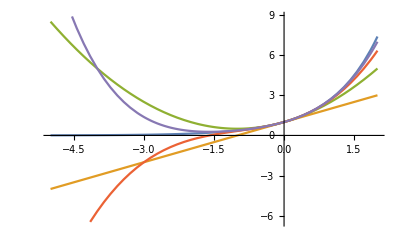

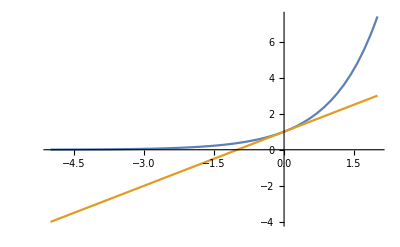

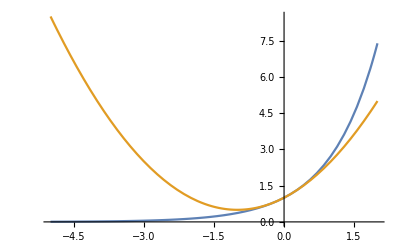

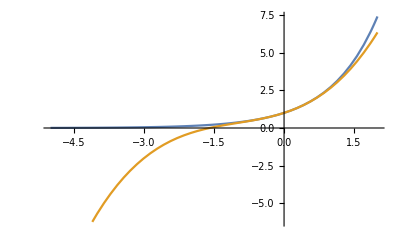

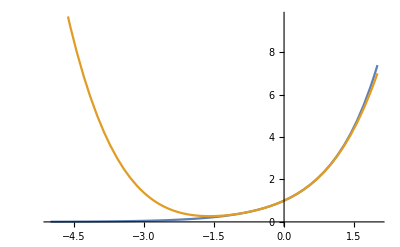

```mathematica
Plot[{f[x],T1[x],T2[x],T3[x],T4[x]},{x,-5,2}]
Plot[{f[x],T1[x]},{x,-5,2}]
Plot[{f[x],T2[x]},{x,-5,2}]
Plot[{f[x],T3[x]},{x,-5,2}]
Plot[{f[x],T4[x]},{x,-5,2}]
```

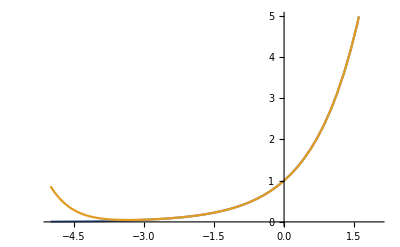

```mathematica
Plot[{f[x],T10[x]},{x,-5,2}]
```

```mathematica
%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%
```

```mathematica
g[x_]=x^(1/3)
T[x_]=Normal[Series[g[x],{x,8,2}]]
```

x^(1/3)

2+1/12 (-8+x)-1/288 (-8+x)^2

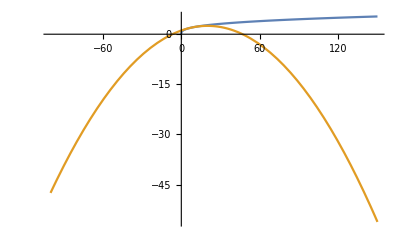

```mathematica
Plot[{g[x],T[x]},{x,-100,150}]
```

```mathematica
N[10/27*7^(-8/3)/6]
```

0.000344263